# Basics of Mathematica

## Getting Started

```mathematica
(*Mathematica does not know what is here. It is just for documentation.*)
2+3
```

5

## Naming syntax

combination of numbers and letters not starting with numbers, as long as you can

```mathematica
myapples = 3
```

3

```mathematica
myapples
```

3

```mathematica
3apples=2
```

Set::write: Tag Times in 3 apples is Protected.

2

```mathematica
3apples
```

3 apples

```mathematica
my_apples=3
```

3

```mathematica
my_apples
```

my_apples

```mathematica
D = 5
```

Set::wrsym: Symbol D is Protected.

5

```mathematica
D
```

D

## Parenthesis

```mathematica
(* [] is used to denote the arguments of functions *)
Exp[2]
```

ⅇ^2

```mathematica
[2+3]*5
```

Syntax::sntxb: Expression cannot begin with "[2+3]*5".

```mathematica
(* () is used to denote priority *)
(2+3)*5
```

25

```mathematica
(* {} give lists *)
{1,2,3}
```

{1,2,3}

## Ask for help!

```mathematica
?Exp
```

```mathematica
?*Integer*
```

```mathematica
?*Bessel*
```

```mathematica
?GaussianIntegers
```

## Make thing look nice

```mathematica
(x^2+2)/(y^3+3)
```

(2+x^2)/(3+y^3)

```mathematica
TeXForm[(x^2+2)/(y^3+3)]
```

\frac{x^2+2}{y^3+3}

```mathematica
(x^2+2)/(y^3+3)
```

## Equal Signs

## Assigning to variables

```mathematica
x=2
```

2

```mathematica
x^2
```

4

```mathematica
x+3
```

5

```mathematica
x=x+1
```

3

```mathematica
y=y+1
```

Hold[1+y]

```mathematica
c=(a=2; b=3;a+b)
```

5

```mathematica
c
```

5

```mathematica
a
```

2

```mathematica
b
```

3

```mathematica
c=(a=2; b=3;a+b);
```

```mathematica
d=(a=2; b=3;a+b;)
```

```mathematica
d
```

```mathematica
d
```

```mathematica
(*swap numbers*)
b=(temp=a;a=b;temp)
```

3

```mathematica
a
```

2

```mathematica
b=Module[{temp1=a},a=b;temp1]
```

2

```mathematica
?Module
```

## Assigning to function

```mathematica
mysquare1[x]=x^2;mysquare1[1]
```

mysquare1[1]

```mathematica
mysquare2[x_]=x^2;mysquare2[1]
```

9

```mathematica
(*remedy 1*)
mysquare3[z_]=z^2;mysquare3[1]
```

1

```mathematica
(*remedy 2*)
x=.
mysquare4[x_]=x^2;mysquare4[2]
```

4

```mathematica
(*remedy 3*)
mysquare5[x_]:=x^2;mysquare5[10]
```

100

```mathematica
g[x_]=x+9;
x=5;
g[10]
```

19

```mathematica
?g
```

```mathematica
g[x_]=x+9;
x=5;
g[10]
```

14

```mathematica
x=.
Simplify[Cos[x]^2+Sin[x]^2]
```

1

```mathematica
mySimplify[sth_]=Simplify[sth]+1;
mySimplify[Cos[x]^2+Sin[x]^2]
```

1+Cos[x]^2+Sin[x]^2

```mathematica
mySimplify[sth_]:=Simplify[sth]+1;
mySimplify[Cos[x]^2+Sin[x]^2]
```

2

```mathematica
f=.
f[x_]:=D[x^2,x]
```

```mathematica
f[x]
```

2 x

```mathematica
Plot[f[x],{x,0,1}]
```

-Graphics-

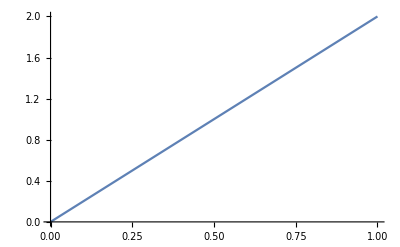

```mathematica
f[x_]=D[x^2,x];
Plot[f[x],{x,0,1}]
```

```mathematica
x=Random[]
```

0.506857

```mathematica
x
```

0.506857

```mathematica
y:=Random[]
```

```mathematica
y
```

0.135585

```mathematica
y
```

0.560219

```mathematica
y
```

0.297211

```mathematica
Timing[1+2]
```

{0.,3}

```mathematica
a==b
```

False

## Lists

```mathematica
list1 = {aa,bb,cc}
```

{aa,bb,cc}

```mathematica
Take[list1,1]
```

{aa}

```mathematica
list1
```

{aa,bb,cc}

```mathematica
Drop[list1,1]
```

{bb,cc}

```mathematica
Take[list1,-1]
```

{cc}

```mathematica
Length[list1]
```

3

```mathematica
comlist={2,{3,4},5}
```

{2,{3,4},5}

```mathematica
Flatten[comlist]
```

{2,3,4,5}